### Codes

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\14燃烧年会

```mathematica
(*Species Specification*)
numReac=2;
numProd=3;
numIntM=6;
numTraS=9;
(*Species Energy, with zero-point correction*)
EReac={-77.299011+-846.512339,-77.299011+-846.486293} ;(*R51sin+C2H2sin,R51tri+C2H2sin*);
EProd={-923.846111,-923.849532,-923.854276}(*CenterP,HeadZigP,SideSiteP*);
EIntM={-923.780458,-923.781024,-923.757510,-923.758102,-923.754122,-923.754633}(*CenterIM1,CenterIM2,HeadZigIM1,HeadZigIM2,SideSiteIM1,SideSiteIM2*);
ETraS={-923.755557,-923.774935,-923.736480,-923.735989,-923.751969,-923.713097,-923.734723,-923.748646,-923.710704}(*Center1-3,HZ1-3,SS1-3*);
E0=EReac⟦1⟧;
EReac=(EReac-E0)*627.51;
EProd=(EProd-E0)*627.51;
EIntM=(EIntM-E0)*627.51;
ETraS=(ETraS-E0)*627.51;
(*Coordinates Settings*)
Emin=Min[EProd]-20;
Emax=Max[ETraS]+20;
xscaling=5;
xmax=xscaling*3 +1;
xmin=-1;
xlength=0.5;
(*PlotStyle Specificatoiin*)
FMT={13,Italic};
LineFMT= Thick; (*Dashed,Thick,CapForm[Round],JoinForm[Round]*)
plotframe={{Style["Energy  (kcal/mol)",17],},{Style["Internal Reaction Coordinates",17],}};
arrowsize=Small;
imageposition=25;
imagesize=3;
color={Red,Green,Blue};(*Center, HeadZig,SideSite*)
(*Check*)
Print[EReac];
Print[EProd];
Print[EIntM];
Print[ETraS];
If [Dimensions[EReac]⟦1⟧== numReac,Print["Number of Reactants, Right"],Print["Number of Reactants, Wrong"]];
If [Dimensions[EProd]⟦1⟧== numProd,Print["Number of Products, Right"],Print["Number of Products, Wrong"]];
If [Dimensions[EIntM]⟦1⟧== numIntM,Print["Number of InterMediates, Right"],Print["Number of InterMediates, Wrong"]];
If [Dimensions[ETraS]⟦1⟧== numTraS,Print["Number of TransitionStates, Right"],Print["Number of TransitionStates, Wrong"]];
(*IM1={{energy},{name},{position},{offset},{picpath},{piclayer}}*)
(*TS1={{energy},{name},{position},{offset},{picpath},{piclayer},{one end,the other end}}*)
Reac[i_]:={{EReac⟦i⟧},{"R"<>ToString[i]},{0,EReac⟦i⟧},{0,-1},{NotebookDirectory[]<>"R"<>ToString[i]<>".tif"},{0,imageposition}};
Prod[i_]:={{EProd⟦i⟧},{"P"<>ToString[i]},{xmax-1,EProd⟦i⟧},{0,-1},{NotebookDirectory[]<>"P"<>ToString[i]<>".tif"},{0,imageposition}};
IntM[i_]:={{EIntM⟦i⟧},{"IM"<>ToString[i]},{(2-Mod[i,2])*xscaling,EIntM⟦i⟧},{0,-1},{NotebookDirectory[]<>"IM"<>ToString[i]<>".tif"},{0,imageposition}};
TraS[i_]:={{ETraS⟦i⟧},{"TS"<>ToString[i]},{(i-0.5)*xscaling,ETraS⟦i⟧},{0,-1},{NotebookDirectory[]<>"TS"<>ToString[i]<>".tif"},{0,imageposition}};
(*Specific Settings of Reac Prod IntM and TranS*)
```

{0.,16.3441}

{-21.8129,-23.9596,-26.9365}

{19.385,19.0299,33.7851,33.4137,35.9111,35.5905}

{35.0107,22.8508,46.9817,47.2898,37.2622,61.6547,48.0842,39.3474,63.1564}

Number of Reactants, Right

Number of Products, Right

Number of InterMediates, Right

Number of TransitionStates, Right

```mathematica
(*Default position is TraS[i]⟦3⟧ which is linking the two nearby stable state, if the following is not specified*)
TraS[1]=Append[TraS[1],{Reac[2]⟦3⟧,IntM[1]⟦3⟧}];
TraS[2]=Append[TraS[2],{IntM[1]⟦3⟧,IntM[2]⟦3⟧}];
TraS[3]=Append[TraS[3],{IntM[2]⟦3⟧,Prod[1]⟦3⟧}];
TraS[4]=Append[TraS[4],{Reac[2]⟦3⟧,IntM[3]⟦3⟧}];
TraS[5]=Append[TraS[5],{IntM[3]⟦3⟧,IntM[4]⟦3⟧}];
TraS[6]=Append[TraS[6],{IntM[4]⟦3⟧,Prod[2]⟦3⟧}];
TraS[7]=Append[TraS[7],{Reac[2]⟦3⟧,IntM[5]⟦3⟧}];
TraS[8]=Append[TraS[8],{IntM[5]⟦3⟧,IntM[6]⟦3⟧}];
TraS[9]=Append[TraS[9],{IntM[6]⟦3⟧,Prod[3]⟦3⟧}];
(*TraS[1]⟦7⟧={Reac[2]⟦3⟧,IntM[1]⟦3⟧};
TraS[2]⟦7⟧={IntM[1]⟦3⟧,IntM[2]⟦3⟧};
TraS[3]⟦7⟧={IntM[2]⟦3⟧,IntM[3]⟦3⟧};
TraS[4]⟦7⟧={IntM[3]⟦3⟧,Prod[1]⟦3⟧};*)
```

```mathematica
(*colorfunctionReac[i_]:=IF[i>2,If[i>4,RGBColor[0,0,1],RGBColor[0,1,0]] ,RGBColor[1,0,0] ];*)
```

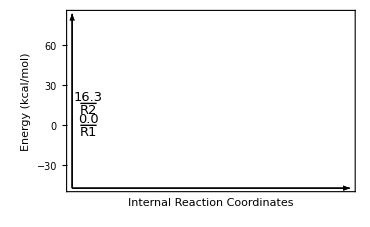

```mathematica
(*colorfunctionReac[i_]:={IF[i>2,If[i>4,aaa=RGBColor[0,0,1],aaa=RGBColor[0,1,0]] ,aaa=RGBColor[1,0,0] ];aaa};*)
ReacPlot[i_]:=Graphics[
{   
{Thick,LineFMT,Line[{{Reac[i]⟦3,1⟧-xlength,Reac[i]⟦3,2⟧},{Reac[i]⟦3,1⟧+xlength,Reac[i]⟦3,2⟧}}]},Text[Style[Reac[i]⟦2,1⟧,FMT],Reac[i]⟦3⟧,Reac[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[Reac[i]⟦1,1⟧,{3,1}],FMT],Reac[i]⟦3⟧,Reac[i]⟦4⟧ ],
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}](*,
Inset[Import[Reac[i]⟦5,1⟧],Reac[i]⟦3⟧-Reac[i]⟦6⟧,Automatic,imagesize]*)
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic},FrameTicksStyle-> 16 ];
Reacimage=Show[Table[ReacPlot[s],{s,numReac}]]
```

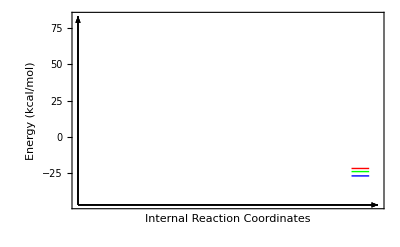

```mathematica
ProdPlot[i_]:=Graphics[
{   
{Thick,LineFMT,color⟦i⟧,Line[{{Prod[i]⟦3,1⟧-xlength,Prod[i]⟦3,2⟧},{Prod[i]⟦3,1⟧+xlength,Prod[i]⟦3,2⟧}}]},(*Text[Style[Prod[i]⟦2,1⟧,FMT,color⟦i⟧],Prod[i]⟦3⟧,Prod[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[Prod[i]⟦1,1⟧,{3,1}],FMT,color⟦i⟧],Prod[i]⟦3⟧,Prod[i]⟦4⟧ ],*)
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}](*,
Inset[Import[Prod[i]⟦5,1⟧],Prod[i]⟦3⟧-Prod[i]⟦6⟧,Automatic,imagesize]*)
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic},FrameTicksStyle-> 16 ];
Prodimage=Show[Table[ProdPlot[s],{s,numProd}]]
```

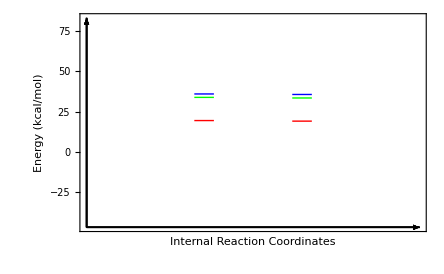

```mathematica
IntMPlot[i_]:=Graphics[
{   
{Thick,LineFMT,color⟦Quotient[i,2.1]+1⟧,Line[{{IntM[i]⟦3,1⟧-xlength,IntM[i]⟦3,2⟧},{IntM[i]⟦3,1⟧+xlength,IntM[i]⟦3,2⟧}}]},(*Text[Style[IntM[i]⟦2,1⟧,color⟦Quotient[i,2.1]+1⟧,FMT],IntM[i]⟦3⟧,IntM[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[IntM[i]⟦1,1⟧,{3,1}],color⟦Quotient[i,2.1]+1⟧,FMT],IntM[i]⟦3⟧,IntM[i]⟦4⟧ ],*)
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}](*,
Inset[Import[IntM[i]⟦5,1⟧],IntM[i]⟦3⟧-IntM[i]⟦6⟧,Automatic,imagesize]*)
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic},FrameTicksStyle-> 16 ];
IntMimage=Show[Table[IntMPlot[s],{s,numIntM}]]
```

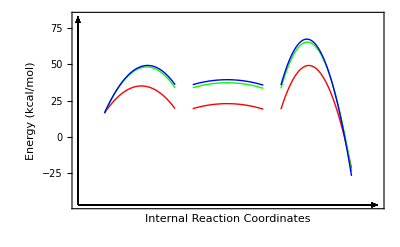

```mathematica
TraSPlot[i_]:=Graphics[
{   (*BSplineCurve[{TraS[i]⟦7,1⟧+{xlength,0},{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦7,2⟧-{xlength,0}},SplineDegree-> 1],*)
(*Text[Style[TraS[i]⟦2,1⟧,color⟦Quotient[i,3.1]+1⟧,FMT],{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦4⟧ *(-1)],
Text[Style[NumberForm[TraS[i]⟦1,1⟧,{3,1}],color⟦Quotient[i,3.1]+1⟧,FMT],{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦4⟧ ],*)
Arrowheads[arrowsize],Arrow[{{xmin,Emin},{xmax,Emin}}],Arrow[{{xmin,Emin},{xmin,Emax}}]
},
PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}];
Curve[i_]:=Interpolation[{TraS[i]⟦7,1⟧+{xlength,0},{TraS[i]⟦7,1,1⟧/2+TraS[i]⟦7,2,1⟧/2,TraS[i]⟦3,2⟧},TraS[i]⟦7,2⟧-{xlength,0}}, InterpolationOrder->2];
TraSCurvePlot[i_]:=Plot[Curve[i][x],{x,TraS[i]⟦7,1,1⟧+xlength,TraS[i]⟦7,2,1⟧-xlength}
,AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,Ticks-> {None,Automatic},PlotStyle-> color⟦Quotient[i,3.1]+1⟧,FrameTicksStyle-> 16 ];
TraSimage=Show[Table[{TraSCurvePlot[s],TraSPlot[s]},{s,numTraS}],PlotRange->{{xmin,xmax},{Emin,Emax}},AxesOrigin->{xmin,Emin},Frame-> {{True,False},{True,False}},FrameLabel->plotframe,AspectRatio-> 1/GoldenRatio,FrameTicks-> {None,Automatic}]
(*Show[Table[TraSPlot[s],{s,numTraS}]]*)
```

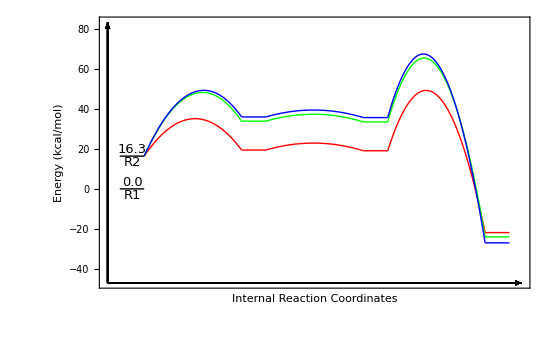

```mathematica
Show[Reacimage,Prodimage,IntMimage,TraSimage]
```